## Write Data to files.

0.000236667 √(0.0000809/a^4+1/a^3)

0.000236667 √(0.734+0.0000809/a^4+0.26463/a^3)

0.000236667 √(0.0000809/a^4+0.26463/a^3+0.734 a^0.3 ⅇ^(0.6 (1-a)))

0.000236667 √(0.0000809/a^4+0.26463/a^3+0.734 a^0.3 ⅇ^(0.9 (1-a)))

0.000236667 √(0.0000809/a^4+0.26463/a^3+0.734 a^0.3 ⅇ^(0.96 (1-a)))

0.000236667 √(0.0000809/a^4+0.26463/a^3+0.734 a^0.3 ⅇ^(1.02 (1-a)))

0.000236667 √(0.0000809/a^4+0.26463/a^3+0.734 a^0.3 ⅇ^(1.32 (1-a)))

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

k

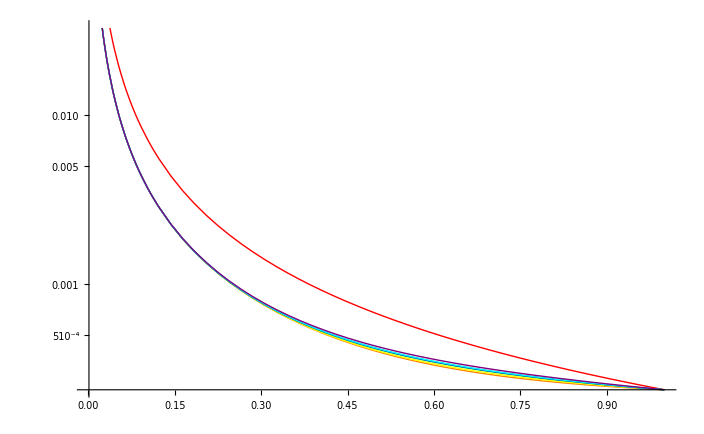

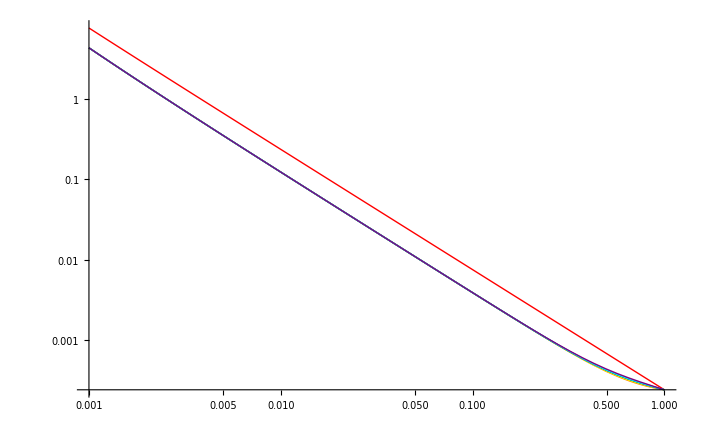

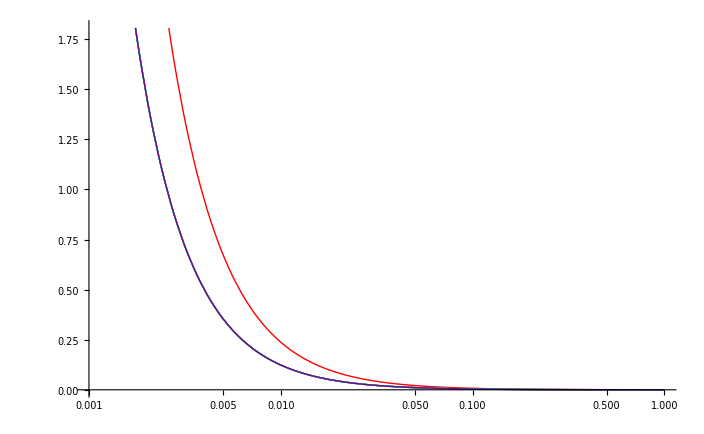

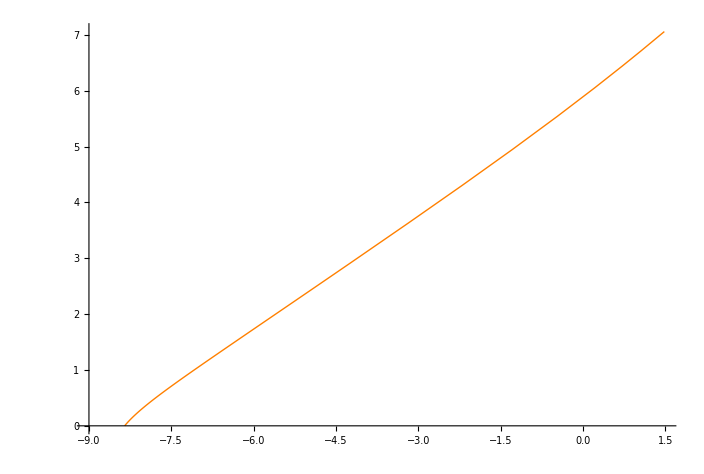

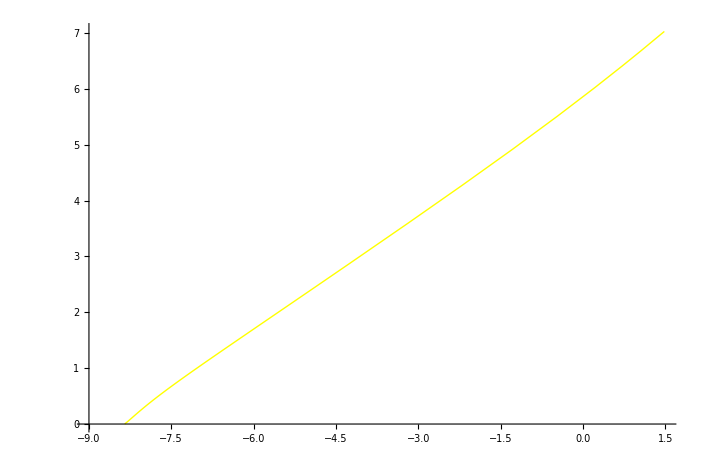

Growth

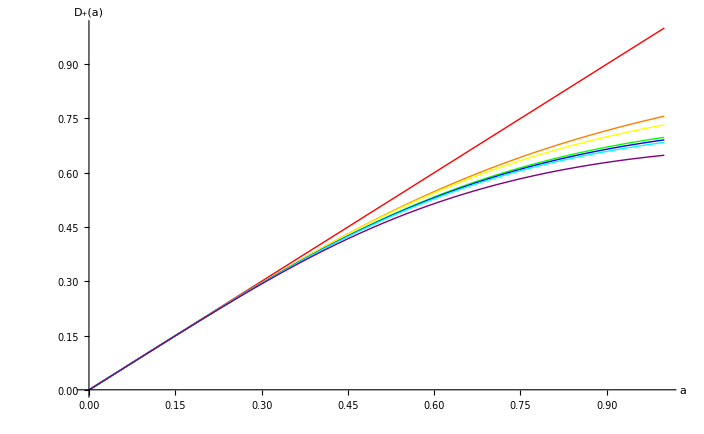

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 41.459  + 55.5417\ ⅈ
 and 38.5744 for the integral and error estimates.

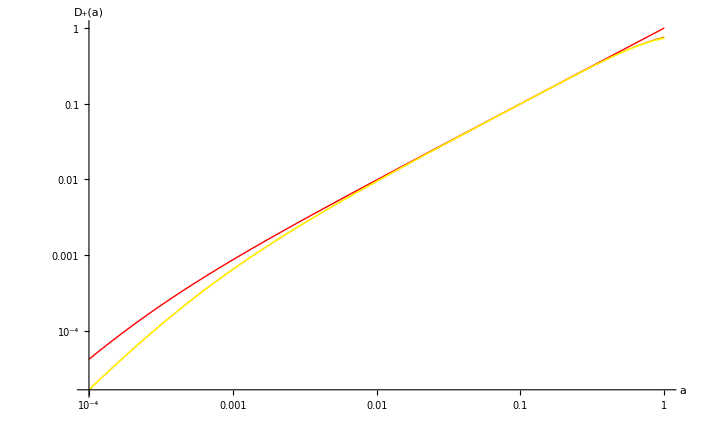

Growth

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

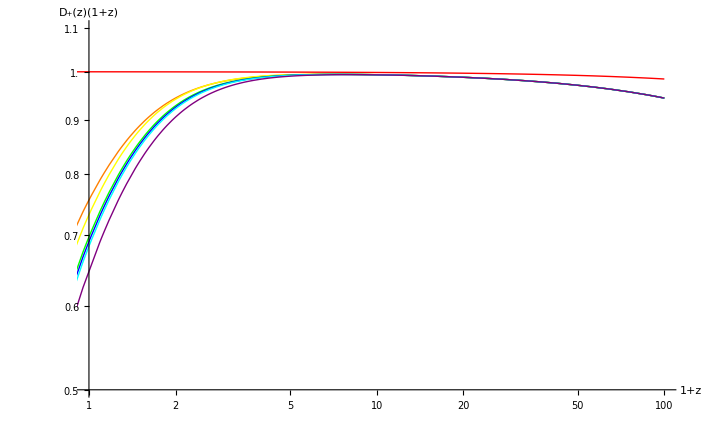

d_H

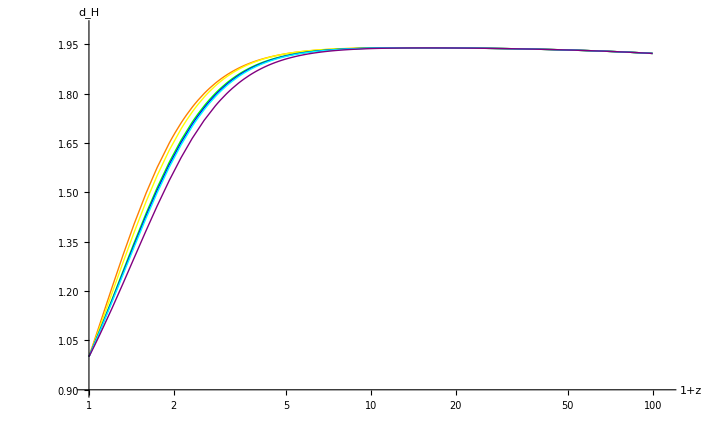

1/d_H

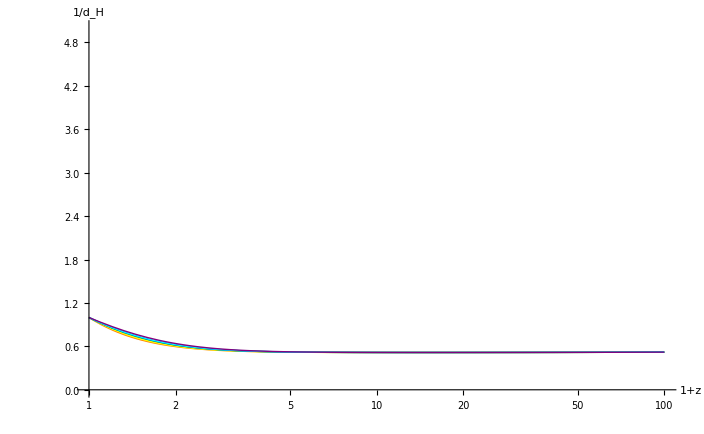

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2][a_]:=Subscript[w, 0]+Subscript[w, a] (1-a);
Subscript[w, 0]=-0.78;
Subscript[w, a]=-0.32;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
h=0.71;
Subscript[H, 0]=(100 h)/300000 ;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;
Subscript[H, s][a_]=Subscript[H, 0] √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4)
Subscript[H, L][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 0]+Subscript[w, a]))Exp[-3 (Subscript[w, a]+0.12) (1-a)])
Subscript[H, 3][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 0]+Subscript[w, a]))Exp[-3 (Subscript[w, a]+0.02) (1-a)])
Subscript[H, 4][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 0]+Subscript[w, a]))Exp[-3 Subscript[w, a] (1-a)])
Subscript[H, 5][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 0]+Subscript[w, a]))Exp[-3 (Subscript[w, a]-0.02) (1-a)])
Subscript[H, 6][a_]=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 0]+Subscript[w, a]))Exp[-3 (Subscript[w, a]-0.12) (1-a)])
Subscript[k, s][a_]=Subscript[H, s][a];kL[a_]=Subscript[H, L][a];Subscript[kDE, 2][a_]=Subscript[H, 2][a];Subscript[kDE, 3][a_]=Subscript[H, 3][a];Subscript[kDE, 4][a_]=Subscript[H, 4][a];Subscript[kDE, 5][a_]=Subscript[H, 5][a];Subscript[kDE, 6][a_]=Subscript[H, 6][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
Subscript[Growth, s][a_]= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 3][a_]=5/2 Subscript[Ω, m0] (Subscript[H, 3][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 3][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 4][a_]=5/2 Subscript[Ω, m0] (Subscript[H, 4][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 4][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 5][a_]=5/2 Subscript[Ω, m0] (Subscript[H, 5][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 5][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 6][a_]=5/2 Subscript[Ω, m0] (Subscript[H, 6][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 6][x])/Subscript[H, 0])^3),{x,0,a}];
(*k~a*)Print[k]
LogPlot[{Subscript[k, s][a],kL[a],Subscript[kDE, 2][a],Subscript[H, 3][a],Subscript[H, 4][a],Subscript[H, 5][a],Subscript[H, 6][a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
LogLogPlot[{Subscript[k, s][a],kL[a],Subscript[kDE, 2][a],Subscript[H, 3][a],Subscript[H, 4][a],Subscript[H, 5][a],Subscript[H, 6][a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
LogLinearPlot[{Subscript[k, s][a],kL[a],Subscript[kDE, 2][a],Subscript[H, 3][a],Subscript[H, 4][a],Subscript[H, 5][a],Subscript[H, 6][a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
(*eg*)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0},PlotStyle->{Orange}]
ParametricPlot[{Log[Subscript[kDE, 2][a]],Log[(Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][a])]},{a,10^-3,1},PlotRange-> Full, AxesOrigin-> {-9,0},PlotStyle->{Yellow}]
(*Growth~a*)Print[Growth]
Plot[{Subscript[Growth, s][a],GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[GrowthDE, 3][a],Subscript[GrowthDE, 4][a],Subscript[GrowthDE, 5][a],Subscript[GrowthDE, 6][a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel-> {a,"D_+(a)"}]
LogLogPlot[{Subscript[Growth, s][a],GrowthL[a],Subscript[GrowthDE, 2][a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow},AxesLabel-> {a,"D_+(a)"}]
(*Growth with respect to 1+z*)
GL[mn_]:=GrowthL[1/mn];GS[mn_]:=Subscript[Growth, s][1/mn];Subscript[GDE, 2][mn_]:=Subscript[GrowthDE, 2][1/mn];Subscript[GDE, 3][mn_]:=Subscript[GrowthDE, 3][1/mn];Subscript[GDE, 4][mn_]:=Subscript[GrowthDE, 4][1/mn];Subscript[GDE, 5][mn_]:=Subscript[GrowthDE, 5][1/mn];Subscript[GDE, 6][mn_]:=Subscript[GrowthDE, 6][1/mn];
Subscript[Lambda, s][mn_]=1/(Subscript[H, s][1/mn]);Subscript[Lambda, L][mn_]=1/(Subscript[H, L][1/mn]);Subscript[Lambda, 2][mn_]=1/(Subscript[H, 2][1/mn]);Subscript[Lambda, 3][mn_]=1/(Subscript[H, 3][1/mn]);Subscript[Lambda, 4][mn_]=1/(Subscript[H, 4][1/mn]);Subscript[Lambda, 5][mn_]=1/(Subscript[H, 5][1/mn]);Subscript[Lambda, 6][mn_]=1/(Subscript[H, 6][1/mn]);
(*LogLogPlot[{GL[mn]/GS[mn], (Subscript[GDE, 2][mn])/GS[mn], (Subscript[GDE, 3][mn])/GS[mn], (Subscript[GDE, 4][mn])/GS[mn], (Subscript[GDE, 5][mn])/GS[mn], (Subscript[GDE, 6][mn])/GS[mn]},{mn,0.1,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotRange->Full,PlotLabel->Growth[1+z]]*)
Print[Growth]
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn) Subscript[GDE, 2][mn],(mn) Subscript[GDE, 3][mn],(mn) Subscript[GDE, 4][mn],(mn) Subscript[GDE, 5][mn],(mn) Subscript[GDE, 6][mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{1,100},{0.5,1.1}},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(**)Print[Subscript[d, H]]
(* (*Too ugly*)
LogPlot[{(Subscript[Lambda, L][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 2][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 3][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 4][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 5][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 6][mn])/(Subscript[Lambda, s][mn])},{mn,10^-2,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
LogLogPlot[{(Subscript[Lambda, L][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 2][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 3][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 4][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 5][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 6][mn])/(Subscript[Lambda, s][mn])},{mn,10^-2,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
*)
LogLinearPlot[{(Subscript[Lambda, L][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 2][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 3][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 4][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 5][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 6][mn])/(Subscript[Lambda, s][mn])},{mn,1,100},PlotRange->{{1,110},{0.9,2}},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
(**)Print[1/Subscript[d, H]]
LogLinearPlot[{(Subscript[H, L][1/mn])/(Subscript[H, s][1/mn]),(Subscript[H, 2][1/mn])/(Subscript[H, s][1/mn]),(Subscript[H, 3][1/mn])/(Subscript[H, s][1/mn]),(Subscript[H, 4][1/mn])/(Subscript[H, s][1/mn]),(Subscript[H, 5][1/mn])/(Subscript[H, s][1/mn]),(Subscript[H, 6][1/mn])/(Subscript[H, s][1/mn])},{mn,1,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","1/d_H"},PlotRange->{0,5}]
```

```mathematica
PowerS=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerspectrumLCDMdataLongrange.dat"];
PowerS
PowerS[[1,1]]
PowerS[[839,1]]
leth=Length[PowerS]
PowerS[[leth,1]]
PowerS[[leth,2]]
```

{{0.0000147064,1.29001×10^8},{0.0000147555,1.27975×10^8},{0.0000148046,1.2695×10^8},{0.0000148538,1.25926×10^8},{0.0000149029,1.24904×10^8},{0.000014952,1.23883×10^8},{0.0000150011,1.22865×10^8},{0.0000150503,1.21851×10^8},{0.0000150994,1.20839×10^8},«4065»,{5.56005,0.751554},{5.57791,0.745433},{5.59576,0.739343},{5.61362,0.733282},{5.63147,0.727245},{5.64933,0.721226},{5.66718,0.715221},{5.68504,0.709225},{5.70289,0.703234}}

0.0000147064

0.000203193

4083

5.70289

0.703234

```mathematica
(*Test the Hubble equation*)
Subscript[H, L][1]/h
Subscript[H, L][0.01]/h
Subscript[H, L][0.001]/h
Subscript[H, L][0.0001]/h
Subscript[H, L][0.00001]/h
Subscript[H, L][0.000001]/h
Subscript[H, 2][0.01]/h
Subscript[H, 2][0.001]/h
```

0.000333118

0.174076

6.19615

345.387

30467.9

3.00305×10^6

0.174075

6.19615

```mathematica
(*
Subscript[a, x]/.FindRoot[0.001==0.00023666666666666665 √(0.0000809/Subscript[a, x]^4+0.26463003372346755/Subscript[a, x]^3+(0.734 ⅇ^(-0.96 (1-Subscript[a, x])))/Subscript[a, x]^1.62) ,{Subscript[a, x],10^-5}]

FindRoot[10==(0.00023666666666666665 √(0.0000809/Subscript[a, x]^4+0.26463003372346755/Subscript[a, x]^3+(0.734 ⅇ^(-0.96 (1-Subscript[a, x])))/Subscript[a, x]^1.62))^2,{Subscript[a, x],10^-5}]*)
(*
LogLinearPlot[{0.734 x^-0.003(1.003004504503377+0.003009013513510131 x+4.513520270265197*^-6 x^2)^-1,0.734 (1.003004504503377+0.003009013513510131 x+4.513520270265197*^-6 x^2)^-1},{x,0.001,1},PlotRange->Full,AxesOrigin-> {0,0.73}]*)
```

```mathematica
aokTabL=Table[Subscript[a, L]/.FindRoot[PowerS[[i,1]]==Subscript[H, L][Subscript[a, L]] ,{Subscript[a, L],10^-6}],{i,1,leth}];
aokTabDE2=Table[Subscript[a, 2]/.FindRoot[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]],{Subscript[a, 2],10^-6}],{i,1,leth}];
aokTabDE3=Table[Subscript[a, 3]/.FindRoot[PowerS[[i,1]]==Subscript[H, 3][Subscript[a, 3]],{Subscript[a, 3],10^-6}],{i,1,leth}];
aokTabDE4=Table[Subscript[a, 4]/.FindRoot[PowerS[[i,1]]==Subscript[H, 4][Subscript[a, 4]],{Subscript[a, 4],10^-6}],{i,1,leth}];
aokTabDE5=Table[Subscript[a, 5]/.FindRoot[PowerS[[i,1]]==Subscript[H, 5][Subscript[a, 5]],{Subscript[a, 5],10^-6}],{i,1,leth}];
aokTabDE6=Table[Subscript[a, 6]/.FindRoot[PowerS[[i,1]]==Subscript[H, 6][Subscript[a, 6]],{Subscript[a, 6],10^-6}],{i,1,leth}];
aokTabL[[1700]]
aokTabDE2[[1700]]
aokTabDE3[[1700]]
aokTabDE4[[1700]]
aokTabDE5[[1700]]
aokTabDE6[[1700]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

0.116016

0.115997

0.116043

0.116053

0.116064

0.11613

```mathematica
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabL(CPL).xls",aokTabL,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabDE2(CPL).xls",aokTabDE2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabDE3(CPL).xls",aokTabDE3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabDE4(CPL).xls",aokTabDE4,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabDE5(CPL).xls",aokTabDE5,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\aokTabDE6(CPL).xls",aokTabDE6,"XLS"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabL(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabDE2(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabDE3(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabDE4(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabDE5(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\aokTabDE6(CPL).xls

```mathematica
(*Normalisation factors Normalised to early time of about a=10^-3*)
frac2=1/(((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[4001]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac3=1/(((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[4001]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac4=1/(((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[4001]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac5=1/(((Subscript[GrowthDE, 5][1])/(Subscript[GrowthDE, 5][aokTabDE5[[4001]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac6=1/(((Subscript[GrowthDE, 6][1])/(Subscript[GrowthDE, 6][aokTabDE6[[4001]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
```

1.03268

1.08387

1.09485

1.1061

1.16659

```mathematica
Qfactor2=Table[{PowerS[[i,1]],frac2((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor3=Table[{PowerS[[i,1]],frac3((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor4=Table[{PowerS[[i,1]],frac4((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor5=Table[{PowerS[[i,1]],frac5((Subscript[GrowthDE, 5][1])/(Subscript[GrowthDE, 5][aokTabDE5[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor6=Table[{PowerS[[i,1]],frac6((Subscript[GrowthDE, 6][1])/(Subscript[GrowthDE, 6][aokTabDE6[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE2vsL(CPL).xls",Qfactor2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE3vsL(CPL).xls",Qfactor3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE4vsL(CPL).xls",Qfactor4,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE5vsL(CPL).xls",Qfactor5,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE6vsL(CPL).xls",Qfactor6,"XLS"]
```

{{0.0000147064,3.09042},{0.0000147555,3.09435},{0.0000148046,3.09825},{0.0000148538,3.10211},{0.0000149029,3.10593},«4073»,{5.63147,1.},{5.64933,1.},{5.66718,1.},{5.68504,1.},{5.70289,1.}}

{{0.0000147064,1.76957},{0.0000147555,1.7734},{0.0000148046,1.77721},{0.0000148538,1.781},{0.0000149029,1.78477},«4073»,{5.63147,1.},{5.64933,1.},{5.66718,1.},{5.68504,1.},{5.70289,1.}}

{{0.0000147064,1.61902},{0.0000147555,1.62274},{0.0000148046,1.62644},{0.0000148538,1.63013},{0.0000149029,1.6338},«4073»,{5.63147,1.},{5.64933,1.},{5.66718,1.},{5.68504,1.},{5.70289,1.}}

{{0.0000147064,1.48981},{0.0000147555,1.49342},{0.0000148046,1.49702},{0.0000148538,1.5006},{0.0000149029,1.50417},«4073»,{5.63147,1.},{5.64933,1.},{5.66718,1.},{5.68504,1.},{5.70289,1.}}

{{0.0000147064,1.05117},{0.0000147555,1.05431},{0.0000148046,1.05743},{0.0000148538,1.06055},{0.0000149029,1.06366},«4073»,{5.63147,1.},{5.64933,1.},{5.66718,1.},{5.68504,1.},{5.70289,1.}}

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\QfactorDE2vsL(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\QfactorDE3vsL(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\QfactorDE4vsL(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\QfactorDE5vsL(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\QfactorDE6vsL(CPL).xls

```mathematica
PowerSDE2=Table[{PowerS[[i,1]]/h,(frac2 ((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(frac3  ((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(frac4 ((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE5=Table[{PowerS[[i,1]]/h,(frac5  ((Subscript[GrowthDE, 5][1])/(Subscript[GrowthDE, 5][aokTabDE5[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE6=Table[{PowerS[[i,1]]/h,(frac6 ((Subscript[GrowthDE, 6][1])/(Subscript[GrowthDE, 6][aokTabDE6[[i]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
(*
PowerSDE2=Table[{PowerS[[i,1]]/h,(Qfactor2[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(Qfactor3[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(Qfactor4[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE5=Table[{PowerS[[i,1]]/h,(Qfactor5[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE6=Table[{PowerS[[i,1]]/h,(Qfactor6[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
*)
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE2(CPL).xls",PowerSDE2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE3(CPL).xls",PowerSDE3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE4(CPL).xls",PowerSDE4,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE5(CPL).xls",PowerSDE5,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE6(CPL).xls",PowerSDE6,"XLS"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSDE2(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSDE3(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSDE4(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSDE5(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSDE6(CPL).xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\CPL\PowerSScale(CPL).xls

P[k]

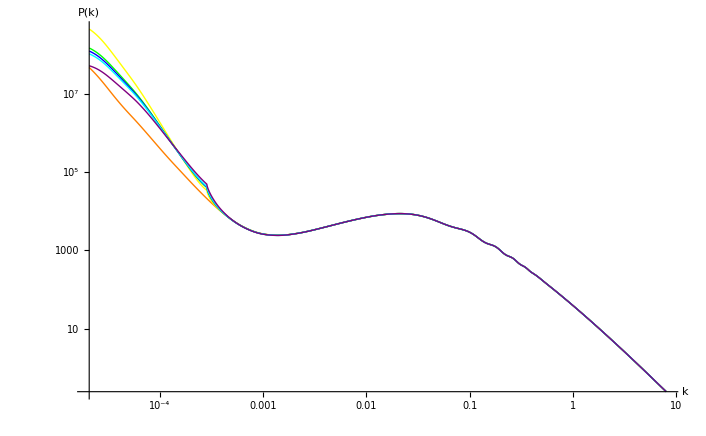

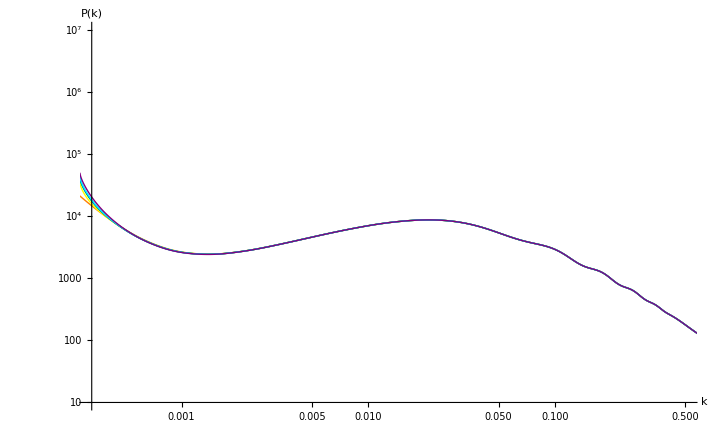

Q[k]

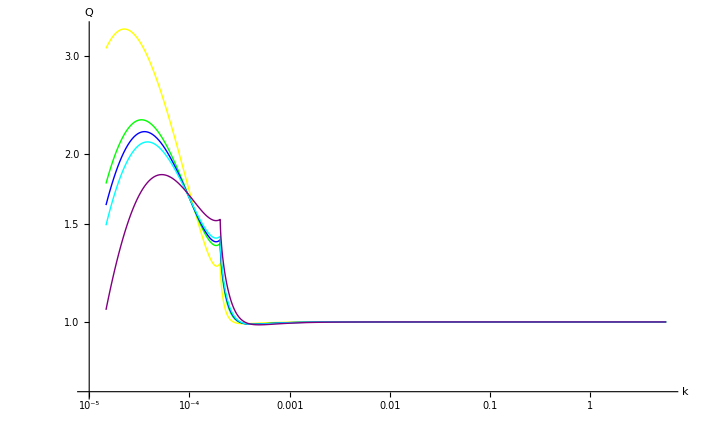

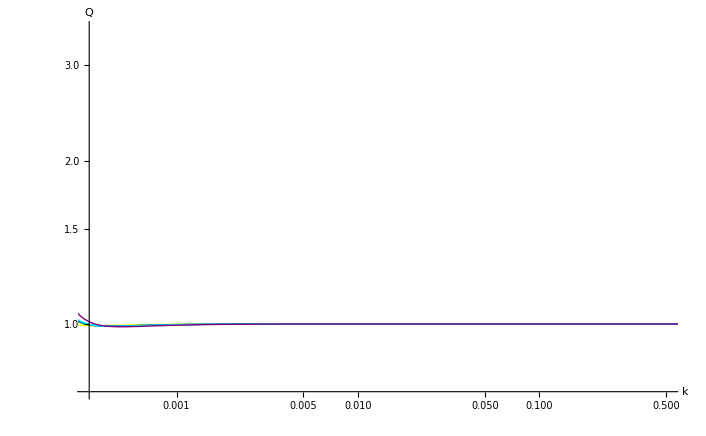

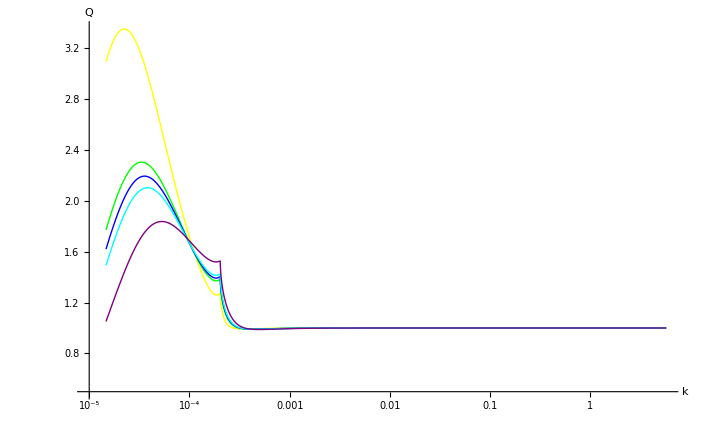

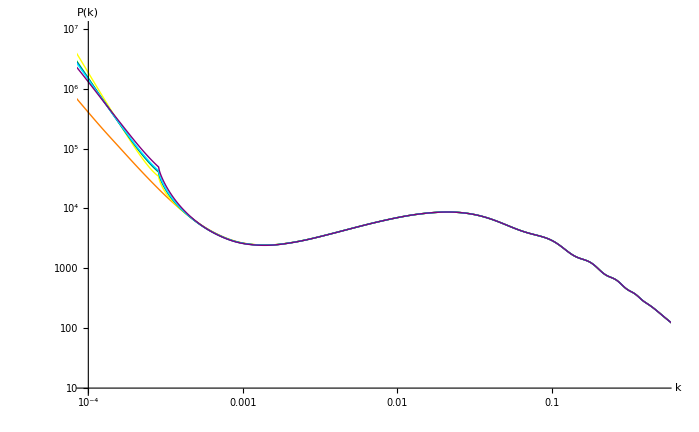

Q[k]

```mathematica
PowerSS=Table[{PowerS[[i,1]]/h,PowerS[[i,2]]  h^3},{i,1,leth}];
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSScale(CPL).xls",PowerSS,"XLS"]
PowerSScale=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSScale(CPL).xls"];
PowerDE2=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE2(CPL).xls"];
PowerDE3=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE3(CPL).xls"];
PowerDE4=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE4(CPL).xls"];
PowerDE5=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE5(CPL).xls"];
PowerDE6=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\PowerSDE6(CPL).xls"];
QfDe2VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE2vsL(CPL).xls"];
QfDe3VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE3vsL(CPL).xls"];
QfDe4VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE4vsL(CPL).xls"];
QfDe5VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE5vsL(CPL).xls"];
QfDe6VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\CPL\\QfactorDE6vsL(CPL).xls"];
Print[P[k]]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4,PowerDE5,PowerDE6},Joined->True, AxesLabel-> {k,P[k]},PlotRange->Automatic,PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple}]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4,PowerDE5,PowerDE6},Joined->True, AxesLabel-> {k,P[k]},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,0.5},{10,10^7}}]
Print[Q[k]]
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},AxesOrigin->{10^-5,0.75}]
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,0.5},{0.75,3.5}}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->Full,AxesOrigin->{10^-5,0.5}]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
```

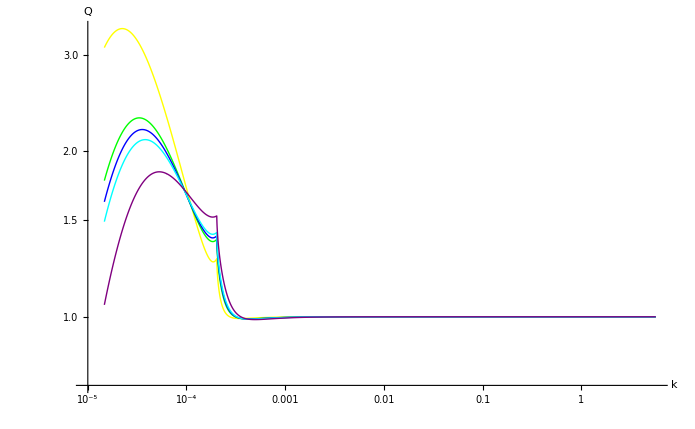

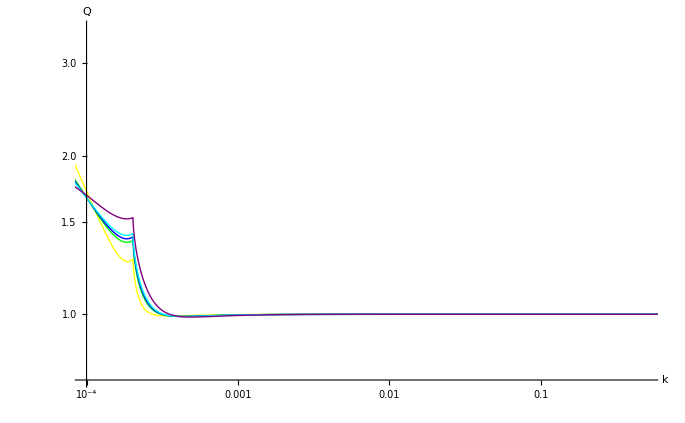

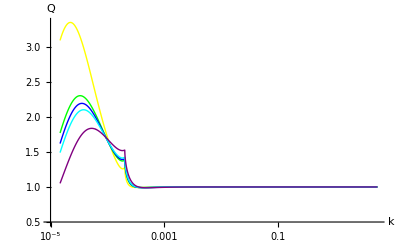

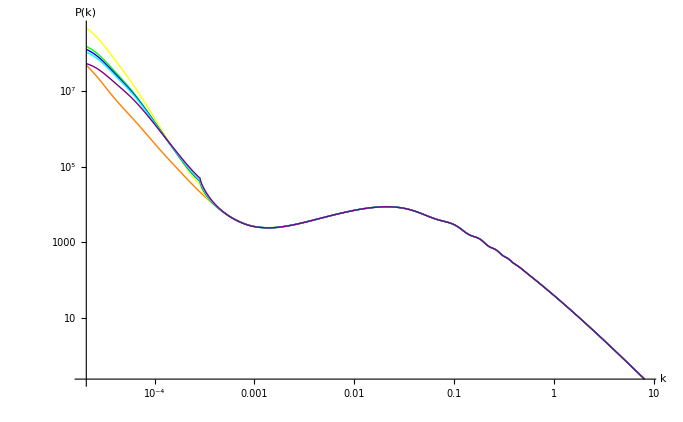

factors k Q vs

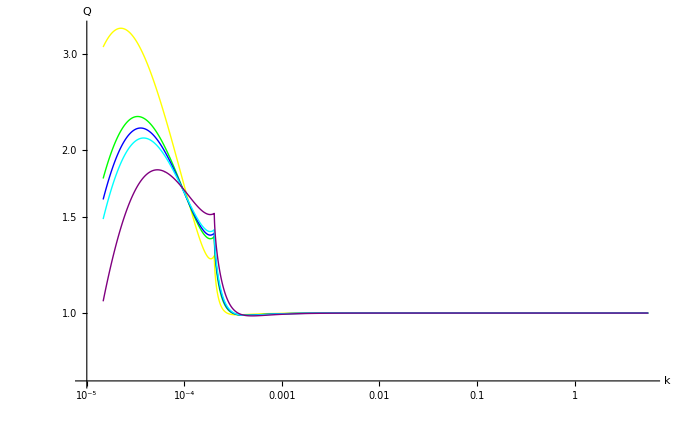

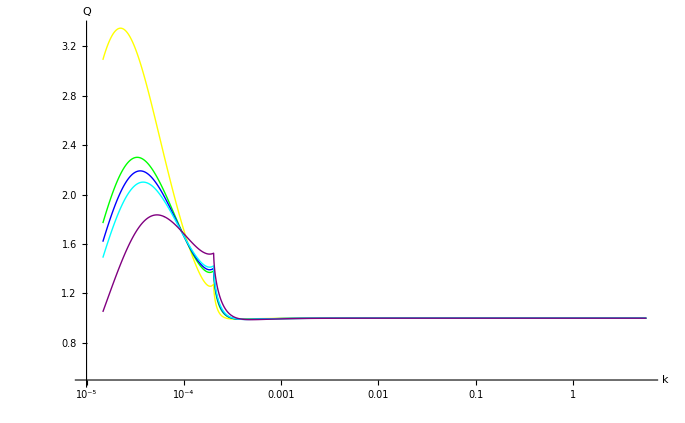

```mathematica
adasde
```